```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/phi3/2loop

```mathematica
<<LiteRed2`
(*<<Mint`*)
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 22:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
convert=Table[ToExpression["topo"<>ToString[i]]-> ToExpression["IF"<>ToString[i]], {i,1,2}];
intfamvoc=Table[ToExpression["IF"<>ToString[i]],{i,1,2}];
```

## Integral family definition topo1

### Preliminaries

```mathematica
family = topo1;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {sp[k1,k1]-m2, sp[k2,k2]-m2, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m2,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m2,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m2}
props ={ "props"->{k1,k2,k1+k2, k1-p,k2+p  }, "every prop is massive with mass^2 "->{m2}, "invariant is p^2 = pp"}
Export["./definitions/props.m",props]
MI={j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]} /. j[topo1,a__] -> topo1[a];
Export["./definitions/masters.m", MI]
```

{-m2+k1·k1,-m2+k2·k2,-m2+k1·k1+2 k1·k2+k2·k2,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2+2 k2·p}

{props→{k1,k2,k1+k2,k1-p,k2+p},every prop is massive with mass^2 →{m2},invariant is p^2 = pp}

./definitions/props.m

./definitions/masters.m

```mathematica
(*(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2},Directory->"topo1"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];

(*Save to disk*)
DiskSave[family];*)
```

```mathematica
intfam//TableForm
```

-m2+k1·k1
-m2+k2·k2
-m2+k1·k1+2 k1·k2+k2·k2
-m2+pp+k1·k1-2 k1·p
-m2+pp+k2·k2+2 k2·p

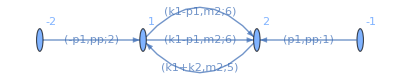

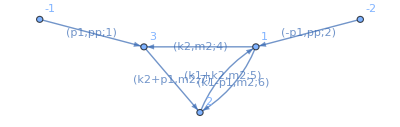

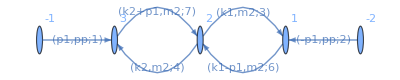

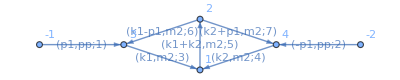

```mathematica
(*Import["./graphs/topo1/all/topo1_2_24.dot"]
Import["./graphs/topo1/all/topo1_3_28.dot"]
Import["./graphs/topo1/all/topo1_3_26.dot"]*)
Import["./graphs/topo1/all/topo1_3_14.dot"]
Import["./graphs/topo1/all/topo1_4_30.dot"]
Import["./graphs/topo1/all/topo1_4_27.dot"]
Import["./graphs/topo1/all/topo1_5_31.dot"]
```

```mathematica
Get["./topo1/topo1"];
```

```mathematica
MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];
(*Put[mis,"./Reduction/FamRed/"<>ToString[family]<>"/"<>"Mi"]
MIs[family];*)
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
(*LiteRed Masters*)
todiff= MIs[family];
```

```mathematica
(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;
```

```mathematica
MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
(*My Masters basis in d=2*)
mybasis= {  j[topo1,0,0,0,1,1],
m2 j[topo1,0,0,1,1,1],
Sqrt[4 m2 -pp]Sqrt[pp] j[topo1,0,1,0,1,1],
(* elliptic sector*)
j[topo1,0,1,1,1,0],
Dinv[j[topo1,0,1,1,1,0],pp],
 m2 √(pp (4 m2-pp))j[topo1,0,1,1,1,1],
pp(pp-4 m2)j[topo1,1,1,0,1,1],
pp j[topo1,1,1,1,1,1]}
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
R = IdentityMatrix[8];
Mpp=(D[R.T,pp].Inverse[R.T]//Simplify) + R.T.MppLiteRed.(Inverse[R.T])//PowerExpand//Simplify;
Mm2=(D[R.T,m2].Inverse[R.T]//Simplify) + R.T.Mm2LiteRed.(Inverse[R.T])//PowerExpand//Simplify;
```

{j[topo1,0,0,0,1,1],m2 j[topo1,0,0,1,1,1],√(4 m2-pp) √pp j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,-1,1,1,2,0]/(2 pp)-j[topo1,0,1,1,1,0]/(2 pp)-1/2 j[topo1,0,1,1,2,0],m2 √((4 m2-pp) pp) j[topo1,0,1,1,1,1],pp (-4 m2+pp) j[topo1,1,1,0,1,1],pp j[topo1,1,1,1,1,1]}

```mathematica
Mpp // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(√(4 m2-pp) √pp) | 0 | (2-d)/(8 m2-2 pp) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
(3 (-2+d)^2)/(2 (m2-pp) (9 m2-pp) pp) | 0 | 0 | -((-3+d) ((4+d) m2+(-4+d) pp))/(2 pp (-9 m2+pp) (-m2+pp)) | -(9 d m2^2-60 m2 pp+10 d m2 pp+12 pp^2-3 d pp^2)/(18 m2^2 pp-20 m2 pp^2+2 pp^3) | 0 | 0 | 0
0 | (-2+d)/(2 √(4 m2-pp) √pp) | 0 | ((-6+d) m2)/(6 √(4 m2-pp) √pp) | -(5 m2 √pp)/(3 √(4 m2-pp)) | (2-d)/(8 m2-2 pp) | 0 | 0
0 | 0 | -(2 (-2+d))/(√(4 m2-pp) √pp) | 0 | 0 | 0 | (-2+d)/(-4 m2+pp) | 0
0 | (2-d)/(12 m2^3-7 m2^2 pp+m2 pp^2) | -((-2+d) (2 m2-pp))/(m2 (3 m2-pp) (4 m2-pp)^(3/2) √pp) | ((-18+7 d) m2-2 (-3+d) pp)/(3 m2 (12 m2^2-7 m2 pp+pp^2)) | (2 pp (m2+pp))/(3 m2 (3 m2-pp) (4 m2-pp)) | (4 (-3+d))/((3 m2-pp) (4 m2-pp)^(3/2) √pp) | (-3+d)/((3 m2-pp) (-4 m2+pp)^2) | (-4+d)/(2 (-3 m2+pp)))

### Elliptic Sector

```mathematica
Mpp[[4;;5,4;;5]]//MatrixForm
Mm2[[4;;5,4;;5]]//MatrixForm
```

(0 | 1
-((-3+d) ((4+d) m2+(-4+d) pp))/(2 pp (-9 m2+pp) (-m2+pp)) | -(9 d m2^2-60 m2 pp+10 d m2 pp+12 pp^2-3 d pp^2)/(18 m2^2 pp-20 m2 pp^2+2 pp^3))

((-3+d)/m2 | -pp/m2
((-3+d) ((4+d) m2+(-4+d) pp))/(2 m2 (m2-pp) (9 m2-pp)) | -(-9 (-8+3 d) m2^2+10 (-2+d) m2 pp+(-4+d) pp^2)/(2 m2 (m2-pp) (9 m2-pp)))

```mathematica
Mm2[[4;;5,4;;5]]/.d -> 2 -2 eps//MatrixForm  // Simplify
```

(-(1+2 eps)/m2 | -pp/m2
((1+2 eps) ((-3+eps) m2+(1+eps) pp))/(m2 (m2-pp) (9 m2-pp)) | (-9 (1+3 eps) m2^2+10 eps m2 pp+(1+eps) pp^2)/(m2 (m2-pp) (9 m2-pp)))

```mathematica
(* 


Picard Fuchs operator in d = 2 dimesnions 


*)
Clear[MI]
(Mpp[[5,4;;5]] /. d-> 2// Together)
pf=d2MI-% .{MI, d1MI}/.m2-> 1
PF=pf  /. {  d1MI -> 1/pp θ, d2MI -> 1/pp^2(θ^2-θ)} /.MI -> 1 /. pp -> λ//Simplify
```

{(3 m2-pp)/((m2-pp) (9 m2-pp) pp),(-9 m2^2+20 m2 pp-3 pp^2)/(pp (9 m2^2-10 m2 pp+pp^2))}

d2MI-(MI (3-pp))/((1-pp) (9-pp) pp)-(d1MI (-9+20 pp-3 pp^2))/(pp (9-10 pp+pp^2))

(2 θ (-5+λ) λ+(-3+λ) λ+θ^2 (9-10 λ+λ^2))/((-9+λ) (-1+λ) λ^2)

```mathematica
pf
```

d2MI-(MI (3-pp))/((1-pp) (9-pp) pp)-(d1MI (-9+20 pp-3 pp^2))/(pp (9-10 pp+pp^2))

```mathematica
(* combine string of operators. F1 will be in the operator, F2 in the ansatz *)
combineOperator = { F1[a__]F2[b__] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b] };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
SolveForAnsatzMUM[point_, maxorder_, indicial_, operator_] := Module[{ansatz, sol0, sol1,coeffSol,der,derpoly,derpolyLog,tmp},
(*first solution*)
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]-> 1};
(* Apply operator to ansatz *)
der=Expand[operator ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;
Clear[ansatz];
(*second solution*)
ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}];
(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}]/. coeffSol;
Return[{sol0,sol1, coeffSol}];
]
```

```mathematica
(* this is the derivative operator in lambada = m2 *)
OP =Collect[(-  Collect[λ^2 (9-10 λ+λ^2)  PF , {θ},Together] /.{ θ θ-> F[θ,θ] ,  θ-> F[θ]}  //Expand) , _F, Factor]
```

-((-3+λ) λ)-2 (-5+λ) λ F[θ]-(-9+λ) (-1+λ) F[θ,θ]

```mathematica
(* generically, if we want to shift λ = λ0 + ρ and expand around ρ ~ 0 (λ ~ λ0), the transformation is the following *)
OPlambda0 =Collect[ Collect[OP   /. {F[θ] -> F[θ] (1 + λ0/ρ) ,F[θ,θ] ->((λ0+ρ) (-λ0 F[θ]+(λ0+ρ) F[θ,θ]))/ρ^2, λ  -> λ0 +ρ }, {_F}, Simplify], {_F} ,Simplify];
(* choose here a point *)
toapply=(OPlambda0/. λ0 ->0/. F -> F1)//Simplify//Expand
(* indicial equation*)
Print["indicial equation:  ",( toapply /. ρ ->  0) == 0 ]
(* indices 0 *)
```

3 ρ-ρ^2+10 ρ F1[θ]-2 ρ^2 F1[θ]-9 F1[θ,θ]+10 ρ F1[θ,θ]-ρ^2 F1[θ,θ]

indicial equation:  -9 F1[θ,θ]==0

```mathematica
(*(* Solution around point 0

 *)
point  = 0;
maxorder =40;
indicial= 0;
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]->0,a[2]-> 1};
(* Apply operator to ansatz *)
der=Expand[toapply ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,0,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;*)
```

```mathematica
(*
point = 0;
maxorder =40;
indicial= 0;
ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
(* Apply operator to ansatz *)
der=Expand[toapply ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
(*If[i===1, Print[Coefficient[derpoly,ρ,i+indicial]/.coeffSol,"  sol ",tmp]];*)
coeffSol = Join[coeffSol,tmp], {i,0,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,0,maxorder}]//. coeffSol;*)
```

```mathematica
(*coeffSol=Thread[Rule[coeffSol[[;;,1]],(coeffSol[[;;,1]]//.coeffSol)]];*)
```

```mathematica
(*sol[point][0]=sol0;
sol[point][1]=sol1;*)
```

```mathematica
Clear[coeffSol](* Solution around MUM point

 *)
point  = 0;
maxorder =40;
indicial= 0;
{sol[point][0],sol[point][1], coeffSol[point]}=SolveForAnsatzMUM[point,maxorder,indicial,toapply];
```

```mathematica
Export["./PERIODS/omega0.m",{sol[point][0],sol[point][1], coeffSol[point]}]
```

./PERIODS/omega0.m

```mathematica
(* check the solution up to the requested order *)
(Series[Expand[toapply sol[point][0]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP, {ρ,0,maxorder-1}]//Normal) /. ρ^(a_)/; a> 99 :> 0
(Series[Expand[toapply sol[point][1]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP//Expand, {ρ,0,maxorder-1}]//Normal)/. ρ^(a_)/; a> 99 :> 0
```

0

0

```mathematica
(* Griffiths transversality condition (don't remember where they come from) *)
Σ = {{0,1},{-1,0}}
(*this is obvious*)
(*Print[{ω0,ω1}.Σ.{ω0,ω1}]*)
griff=Collect[Series[{ω0,ω1}.Σ.{dω0,dω1}   /. {ω0 -> (sol[point][0] /. extractPolySol),ω1 -> (sol[point][1] /. extractPolySol),dω0->  D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP/. log -> L) ,ρ],dω1-> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L} ,{ ρ, 0,21}]//Normal, {ρ}, Together];
Series[(n[0]+n[1]ρ + n[2]ρ^2 + n[3] ρ^3)/((-1+ρ) (-9+ ρ)ρ), {ρ,0,21}] //Expand //Normal ;
Collect[%, {ρ}] /. {n[0] -> 9, n[1] -> 0, n[2] -> 0, n[3]->0};
Print["check the transversality condition:  ",griff-%];
gtc=(n[0]+n[1]ρ + n[2]ρ^2 + n[3] ρ^3)/((-1+ρ) (-9+ ρ)ρ)/. {n[0] -> 9, n[1] -> 0, n[2] -> 0, n[3]-> 0}//Simplify//Factor
{ω0,ω1}.Σ.{dω0,dω1}==gtc
repl=Solve[% /. dω0 ω1 -> V  ,V] /. V -> dω0 ω1  //Flatten
```

{{0,1},{-1,0}}

check the transversality condition:  0

9/((-9+ρ) (-1+ρ) ρ)

dω1 ω0-dω0 ω1==9/((-9+ρ) (-1+ρ) ρ)

{dω0 ω1→-9/((-9+ρ) (-1+ρ) ρ)+dω1 ω0}

```mathematica
(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1,  ω1/ω0},{0,1}}
Wss = {{ω0,0},{dω0,gtc/ω0}}
Wss.Wu /. repl//Simplify
```

{{1,ω1/ω0},{0,1}}

{{ω0,0},{dω0,9/((-9+ρ) (-1+ρ) ρ ω0)}}

{{ω0,ω1},{dω0,dω1}}

```mathematica
InvWss=Inverse[Wss]//Simplify
```

{{1/ω0,0},{-1/9 dω0 (-9+ρ) (-1+ρ) ρ,1/9 (-9+ρ) (-1+ρ) ρ ω0}}

```mathematica
Print["new basis is J,  I = Wss J"]
```

new basis is J,  I = Wss J

```mathematica
(*(Solve[(pf /. m2 -> λ /. λ ->  ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten)*)
```

```mathematica
Export["./PERIODS/d2omega0.m",Solve[(pf /. pp -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten]
```

./PERIODS/d2omega0.m

```mathematica
d2omega0=Solve[(pf /. pp -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten
```

{d2ω0→(-9 dω0+20 dω0 ρ-3 dω0 ρ^2+3 ω0-ρ ω0)/((-9+ρ) (-1+ρ) ρ)}

```mathematica
derinvWss=D[InvWss,ρ]  +(InvWss /. dω0 -> d2ω0  /. 1/ω0 ->( -1/uω0^2 )dω0 /. ω0-> dω0  /. uω0 -> ω0 ) /.((Solve[(pf /. pp -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten) //Simplify)//Simplify
```

{{-dω0/ω0^2,0},{1/9 (-3+ρ) ω0,1/9 (dω0 ρ (9-10 ρ+ρ^2)+(9-20 ρ+3 ρ^2) ω0)}}

```mathematica
(*derinvWss.Wss//MatrixForm*)
```

```mathematica
HomogeneousPart=Mpp[[4;;5,4;;5]] /. d-> 2-2eps/. m2-> 1  /.pp ->λ  /. λ ->  ρ// Apart;
(*derinvWss.Wss // Simplify
InvWss.HomogeneousPart.Wss /. m2 ->λ  /. λ ->   ρ// Simplify *)
NewHomogDerBasis=(derinvWss.Wss // Simplify)+InvWss.HomogeneousPart.Wss /. pp ->λ  /. λ ->  ρ //Expand  //Simplify  ;
NewHomogDerBasis={{eps,0},{0,1}}.NewHomogDerBasis.{{1/eps,0},{0,1}}  // Simplify;
HomogeneousPart /. eps -> 0 // Simplify
(* there is only a total derivative left *)
NewHomogDerBasis   /. eps -> 0// MatrixForm
```

{{0,1},{(3-ρ)/(9 ρ-10 ρ^2+ρ^3),1/(1-ρ)+1/(9-ρ)-1/ρ}}

(0 | 0
1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)-(-5+3 ρ) ω0) | 0)

```mathematica
1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)-(-5+3 ρ) ω0)//Simplify
```

1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)+(5-3 ρ) ω0)

```mathematica
D[1/9ω0^2   (9+10 ρ-3 ρ^2)/2,ρ]//Simplify
```

-1/9 (-5+3 ρ) ω0^2

```mathematica
Id1=IdentityMatrix[3];
AA=Wss;
Id2=IdentityMatrix[3];
T=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Id1=IdentityMatrix[3];
AA=InvWss;
Id2=IdentityMatrix[3];
Tinv=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Zeros1=ConstantArray[0,{3,3}];
AA=derinvWss;
Zeros2=ConstantArray[0,{3,3}];
derTinv=ArrayFlatten[{{Zeros1,0,0},{0,AA,0},{0,0,Zeros2}}];
eps1=IdentityMatrix[4]eps^2;
AA=eps;
eps2=IdentityMatrix[3]eps^2;
EPS=ArrayFlatten[{{eps1,0,0},{0,AA,0},{0,0,eps2}}];
```

```mathematica
(*first rotation by semi - simple blah blah *)
T1 = T;
T1Inv =Tinv;
T1derInv = derTinv;
```

```mathematica
Mpp /. m2 -> 1 /. pp -> ρ /. d-> 2 -2 eps//Simplify
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-(2 eps)/(√(-((-4+ρ) ρ))),0,eps/(4-ρ),0,0,0,0,0},{0,0,0,0,1,0,0,0},{(6 eps^2)/(ρ (9-10 ρ+ρ^2)),0,0,-((1+2 eps) (-3+eps+ρ+eps ρ))/((-9+ρ) (-1+ρ) ρ),(-9+20 ρ-3 ρ^2+eps (9+10 ρ-3 ρ^2))/(ρ (9-10 ρ+ρ^2)),0,0,0},{0,-eps/(√(-((-4+ρ) ρ))),0,(-2-eps)/(3 √(-((-4+ρ) ρ))),-(5 √ρ)/(3 √(4-ρ)),eps/(4-ρ),0,0},{0,0,(4 eps)/(√(-((-4+ρ) ρ))),0,0,0,-(2 eps)/(-4+ρ),0},{0,(2 eps)/(12-7 ρ+ρ^2),(2 eps (-2+ρ))/((4-ρ)^(3/2) (-3+ρ) √ρ),(2 (-2+ρ+eps (-7+2 ρ)))/(3 (12-7 ρ+ρ^2)),(2 ρ (1+ρ))/(3 (-4+ρ) (-3+ρ)),(4 (1+2 eps))/((4-ρ)^(3/2) (-3+ρ) √ρ),(1+2 eps)/((-4+ρ)^2 (-3+ρ)),(1+eps)/(3-ρ)}}

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1 /. m2 -> 1/. pp ->λ  /. λ ->  ρ  /. d-> 2 -2 eps //Expand  //Simplify;
```

```mathematica
(* rescale epsilon dependence *)
newMpp[2] =EPS.newMpp[1] .Inverse[EPS] // Simplify ;
newMpp[2][[4;;5,4;;5]]  // MatrixForm
```

(0 | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2)
1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)-(-5+3 ρ+2 eps (1+ρ)) ω0) | (eps (9+10 ρ-3 ρ^2))/((-9+ρ) (-1+ρ) ρ))

```mathematica
newMpp[2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | 1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)-(-5+3 ρ+2 eps (1+ρ)) ω0) | (eps (9+10 ρ-3 ρ^2))/((-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (-5 dω0 ρ-(2+eps) ω0)/(3 √(-((-4+ρ) ρ))) | -(15 eps)/((-9+ρ) (-1+ρ) √(-((-4+ρ) ρ)) ω0) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | (2 eps)/(12-7 ρ+ρ^2) | (2 eps (-2+ρ) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (2 (dω0 ρ (1+ρ)+(-2+ρ+eps (-7+2 ρ)) ω0))/(3 (-4+ρ) (-3+ρ)) | (6 eps (1+ρ))/((-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ) ω0) | (4 (1+2 eps) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (1+2 eps)/((-4+ρ)^2 (-3+ρ)) | (1+eps)/(3-ρ))

```mathematica
(*
Id1=IdentityMatrix[3];
AA={{1,0},{f[ρ],1}}
Id2=IdentityMatrix[3];
R=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
ansatz=D[Inverse[R],ρ].R + Inverse[R].newMM2.R;
ansatz[[4;;5, ;;5]]  /. eps -> 0//MatrixForm
*)
```

```mathematica
Id1=IdentityMatrix[3];
AA={{1,0},{f[ρ],1}} /. f[ρ] ->  1/9ω0^2   (9+10 ρ-3 ρ^2)/2
Id2=IdentityMatrix[3];
R=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Id1=IdentityMatrix[3];
AA=Inverse[AA] // Simplify;
Id2=IdentityMatrix[3];
Rinv=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Zeros1=ConstantArray[0,{3,3}];
AA=AA -IdentityMatrix[2];
AA=D[AA,ρ]  +(AA/. ω0^2 -> 2 ω0 dω0 ) /.((Solve[(pf /. pp -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten) //Simplify)//Simplify
Zeros2=ConstantArray[0,{3,3}];
derRinv=ArrayFlatten[{{Zeros1,0,0},{0,AA,0},{0,0,Zeros2}}];
```

{{1,0},{1/18 (9+10 ρ-3 ρ^2) ω0^2,1}}

{{0,0},{1/9 ω0 (dω0 (-9-10 ρ+3 ρ^2)+(-5+3 ρ) ω0),0}}

```mathematica
(*total derivative  *)
T2 = R;
T2Inv =Rinv;
T2derInv = derRinv;
newMpp[3]=(T2derInv.T2 //Simplify)+T2Inv.newMpp[2].T2 /. m2 ->1 /. pp ->λ  /. λ ->  ρ  /. d-> 2 -2 eps //Expand  //Simplify;
```

```mathematica
T1derInv
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,-dω0/ω0^2,0,0,0,0},{0,0,0,1/9 (-3+ρ) ω0,1/9 (dω0 ρ (9-10 ρ+ρ^2)+(9-20 ρ+3 ρ^2) ω0),0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Mpp
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{(-2+d)/(√(4 m2-pp) √pp),0,(2-d)/(8 m2-2 pp),0,0,0,0,0},{0,0,0,0,1,0,0,0},{(3 (-2+d)^2)/(2 (m2-pp) (9 m2-pp) pp),0,0,-((-3+d) ((4+d) m2+(-4+d) pp))/(2 pp (-9 m2+pp) (-m2+pp)),-(9 d m2^2-60 m2 pp+10 d m2 pp+12 pp^2-3 d pp^2)/(18 m2^2 pp-20 m2 pp^2+2 pp^3),0,0,0},{0,(-2+d)/(2 √(4 m2-pp) √pp),0,((-6+d) m2)/(6 √(4 m2-pp) √pp),-(5 m2 √pp)/(3 √(4 m2-pp)),(2-d)/(8 m2-2 pp),0,0},{0,0,-(2 (-2+d))/(√(4 m2-pp) √pp),0,0,0,(-2+d)/(-4 m2+pp),0},{0,(2-d)/(12 m2^3-7 m2^2 pp+m2 pp^2),-((-2+d) (2 m2-pp))/(m2 (3 m2-pp) (4 m2-pp)^(3/2) √pp),((-18+7 d) m2-2 (-3+d) pp)/(3 m2 (12 m2^2-7 m2 pp+pp^2)),(2 pp (m2+pp))/(3 m2 (3 m2-pp) (4 m2-pp)),(4 (-3+d))/((3 m2-pp) (4 m2-pp)^(3/2) √pp),(-3+d)/((3 m2-pp) (-4 m2+pp)^2),(-4+d)/(2 (-3 m2+pp))}}

```mathematica
newMpp[3][[4;;5]]//Simplify //MatrixForm//Simplify
```

(0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0)

```mathematica
newMpp[3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | -(10 dω0 ρ (9-10 ρ+ρ^2)+eps (63+30 ρ-13 ρ^2) ω0+4 (9-10 ρ+ρ^2) ω0)/(6 (-9+ρ) (-1+ρ) √(-((-4+ρ) ρ))) | -(15 eps)/((-9+ρ) (-1+ρ) √(-((-4+ρ) ρ)) ω0) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | (2 eps)/(12-7 ρ+ρ^2) | (2 eps (-2+ρ) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (2 dω0 ρ (9-ρ-9 ρ^2+ρ^3)+eps (-117+195 ρ-47 ρ^2+ρ^3) ω0+2 (-18+29 ρ-12 ρ^2+ρ^3) ω0)/(3 (-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ)) | (6 eps (1+ρ))/((-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ) ω0) | (4 (1+2 eps) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (1+2 eps)/((-4+ρ)^2 (-3+ρ)) | (1+eps)/(3-ρ))

```mathematica
R=IdentityMatrix[8];
R[[6,4]] =(5 √((4-ρ) ρ))/(3 (-4+ρ))ω0[ρ]  + g4[ρ] ;
Rinv = Inverse[R];
DRinv = D[Rinv, ρ];
newMpp[4] = (DRinv.R //Simplify)+Rinv.newMpp[3].R /. m2 -> 1/. pp ->λ  /. λ ->  ρ  /. d-> 2 -2 eps /. ω0[ρ] ->ω0 /.ω0'[ρ] -> dω0  //Expand  //Simplify;
newMpp[4]/. eps -> 0;
(*-(10 dω0 ρ (1-10 ρ+9 ρ^2)+(6-60 ρ+54 ρ^2) ω0+6 √(-1+4 ρ) (1-10 ρ+9 ρ^2) g4'[ρ])/(6 √(-1+4 ρ) (1-10 ρ+9 ρ^2))//FullSimplify//Expand*)
```

```mathematica
Collect[newMpp[4][[;;6]] /. ω0[ρ] ->ω0 /.ω0'[ρ] -> dω0 //Simplify, {ω0,dω0 }] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | -(2 (-1+2 eps) √(-((-4+ρ) ρ)) (1+ρ) (9-10 ρ+ρ^2) ω0)/(3 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)+(3 eps (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]-6 (-4+ρ)^2 ρ (9-10 ρ+ρ^2) g4'[ρ])/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0)

```mathematica
(2 ρ (1+ρ) ω0)/(3 (-((-4+ρ) ρ))^(3/2))-g4'[ρ]
```

(2 ρ (1+ρ) ω0)/(3 (-((-4+ρ) ρ))^(3/2))-g4'[ρ]

```mathematica
newMpp[4][[;;]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (3 eps (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]-2 (9-10 ρ+ρ^2) (2 (-1+2 eps) √(-((-4+ρ) ρ)) (1+ρ) ω0+3 (-4+ρ)^2 ρ g4'[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | (2 eps)/(12-7 ρ+ρ^2) | (2 eps (-2+ρ) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (ρ (2 dω0 ρ (-36+13 ρ+35 ρ^2-13 ρ^3+ρ^4)+eps (108-497 ρ+343 ρ^2-51 ρ^3+ρ^4) ω0+2 (-18-34 ρ+67 ρ^2-16 ρ^3+ρ^4) ω0)+12 (1+2 eps) √(-((-4+ρ) ρ)) (9-10 ρ+ρ^2) g4[ρ])/(3 (-9+ρ) (-4+ρ)^2 (-3+ρ) (-1+ρ) ρ) | (6 eps (1+ρ))/((-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ) ω0) | (4 (1+2 eps) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (1+2 eps)/((-4+ρ)^2 (-3+ρ)) | (1+eps)/(3-ρ))

```mathematica
g4def = g4'[ρ]->(2 ρ (1+ρ) ω0)/(3 (((4-ρ) ρ))^(3/2));
```

```mathematica
newMpp[4]=newMpp[4] /.g4def /.√(-((-4+ρ) ρ)) -> √((4-ρ) ρ)/. 1/√(-((-4+ρ) ρ)) -> 1/√((4-ρ) ρ)/. 1/(-((-4+ρ) ρ))^(3/2) -> -I/(((4-ρ)ρ)^(3/2))//Simplify;
% //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | -(eps (8 ρ (9-ρ-9 ρ^2+ρ^3) ω0+3 √(-((-4+ρ) ρ)) (36+13 ρ-2 ρ^2+ρ^3) g4[ρ]))/(6 (-9+ρ) (-1+ρ) (-((-4+ρ) ρ))^(3/2)) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | (2 eps)/(12-7 ρ+ρ^2) | -(2 ⅈ eps (-2+ρ) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (ρ (2 dω0 ρ (-36+13 ρ+35 ρ^2-13 ρ^3+ρ^4)+eps (108-497 ρ+343 ρ^2-51 ρ^3+ρ^4) ω0+2 (-18-34 ρ+67 ρ^2-16 ρ^3+ρ^4) ω0)+12 (1+2 eps) √(-((-4+ρ) ρ)) (9-10 ρ+ρ^2) g4[ρ])/(3 (-9+ρ) (-4+ρ)^2 (-3+ρ) (-1+ρ) ρ) | (6 eps (1+ρ))/((-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ) ω0) | -(4 ⅈ (1+2 eps) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (1+2 eps)/((-4+ρ)^2 (-3+ρ)) | (1+eps)/(3-ρ))

### Shift d -> d+2

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{pp,m12,m22,m32,m42,m52},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {sp[k1,k1]-m12, sp[k2,k2]-m22, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m32,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m42,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m52}
```

{-m12+k1·k1,-m22+k2·k2,-m32+k1·k1+2 k1·k2+k2·k2,-m42+pp+k1·k1-2 k1·p,-m52+pp+k2·k2+2 k2·p}

```mathematica
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[familyAllMass,intfam,{k1,k2},Directory->"topoAllMass"]

GenerateIBP[familyAllMass];

AnalyzeSectors[familyAllMass];

FindSymmetries[familyAllMass];

(*Save to disk*)
DiskSave[familyAllMass];
```

familyAllMass is valid basis. The definitions of the basis will be saved in "topoAllMass" directory.
    Ds[familyAllMass] — denominators,
    SPs[familyAllMass] — scalar products involving loop momenta,
    LMs[familyAllMass] — loop momenta,
    EMs[familyAllMass] — external momenta,
    Parameters[familyAllMass] — parameters (invariants, masses, dimension),
    Toj[familyAllMass] — rules to transform scalar products to denominators,
    CutDs[familyAllMass] — flag vector of cut denominators.

familyAllMass

Identities are generated.
    IBP[familyAllMass] — integration-by-part identities,
    LI[familyAllMass] — Lorentz invariance identities.

Found 8(24) zero(nonzero) sectors out of 32.
    ZeroSectors[familyAllMass] — zero sectors,
    NonZeroSectors[familyAllMass] — nonzero sectors,
    SimpleSectors[familyAllMass] — simple sectors (no nonzero subsectors),
    BasisSectors[familyAllMass] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[familyAllMass] — a rule to nullify all zero j[familyAllMass…],
    CutDs[familyAllMass] — a flag list of cut denominators (1=cut).

Found 0 mapped sectors and 24 unique sectors.
    UniqueSectors[familyAllMass] — unique sectors.
    MappedSectors[familyAllMass] — mapped sectors.
    SR[familyAllMass][…] — symmetry relations for j[familyAllMass,…] from UniqueSectors[familyAllMass].
    jSymmetries[familyAllMass,…] — symmetry rules for the sector js[familyAllMass,…] in UniqueSectors[familyAllMass].
    jRules[familyAllMass,…] — reduction rules for j[familyAllMass,…] from MappedSectors[familyAllMass].
    SectorsMappings[familyAllMass] gives the list of mappings of all sectors from MappedSectors[familyAllMass] to UniqueSectors[familyAllMass].

```mathematica
intfam  = {SP[k1,k1]-m12, SP[k2,k2]-m22, SP[k1,k1]+SP[k2,k2] + 2 SP[k1,k2]-m32,SP[k1,k1]+SP[p,p] - 2 SP[k1,p]-m42,SP[k2,k2]+SP[p,p] +2 SP[k2,p]-m52}
```

{-m12+SP[k1,k1],-m22+SP[k2,k2],-m32+SP[k1,k1]+2 SP[k1,k2]+SP[k2,k2],-m42+SP[k1,k1]-2 SP[k1,p]+SP[p,p],-m52+SP[k2,k2]+2 SP[k2,p]+SP[p,p]}

```mathematica
propsFull
```

propsFull

```mathematica
propsFull = Sum[intfam[[i]]u[ToExpression["m"<>ToString[i]<>"2"]], {i,1,5}];
delta = Coefficient[propsFull, SP[k1,k1]]Coefficient[propsFull, SP[k2,k2]]-Coefficient[propsFull, SP[k1,k2]]Coefficient[propsFull, SP[k1,k2]]/4//Expand //Simplify
```

u[m32] u[m42]+u[m22] (u[m32]+u[m42])+u[m32] u[m52]+u[m42] u[m52]+u[m12] (u[m22]+u[m32]+u[m52])

```mathematica
mybasisd2= {  j[topo1,0,0,0,1,1],
m2 j[topo1,0,0,1,1,1],
Sqrt[4 m2 -pp]Sqrt[pp] j[topo1,0,1,0,1,1],
(* elliptic sector*)
j[topo1,0,1,1,1,0],
Dinv[j[topo1,0,1,1,1,0],pp],
(* rest *)
 m2 √(pp (4 m2-pp))j[topo1,0,1,1,1,1],
pp(pp-4 m2)j[topo1,1,1,0,1,1],
 eps(3-d)/(6-d)^2 pp j[topo1,1,1,1,1,1]}
```

{j[topo1,0,0,0,1,1],m2 j[topo1,0,0,1,1,1],√(4 m2-pp) √pp j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,-1,1,1,2,0]/(2 pp)-j[topo1,0,1,1,1,0]/(2 pp)-1/2 j[topo1,0,1,1,2,0],m2 √((4 m2-pp) pp) j[topo1,0,1,1,1,1],pp (-4 m2+pp) j[topo1,1,1,0,1,1],((3-d) eps pp j[topo1,1,1,1,1,1])/(6-d)^2}

```mathematica
mybasis=Join[IBPReduce[((  (2^2)/(6-d)^2 delta mybasisd2[[;;7]]//Expand )/.topo1 -> familyAllMass)  //.{ u[a_]j[smth__] :> Dinv[j[smth],a],u[a_]^2j[smth__] :> Dinv[Dinv[j[smth],a],a]} /. familyAllMass -> topo1]//Simplify,{mybasisd2[[8]]}];
```

```mathematica
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
invT = Inverse[T]//Simplify;
Mpp=(D[T,pp].Inverse[T]//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(D[T,m2].Inverse[T]//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;
```

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1 /. m2 -> 1/. pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
(* rescale epsilon dependence *)
newMpp[2] =EPS.newMpp[1] .Inverse[EPS] // Simplify ;
newMpp[2][[4;;5,4;;5]]  // MatrixForm
```

(0 | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2)
1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)-(-5+3 ρ+2 eps (1+ρ)) ω0) | (eps (9+10 ρ-3 ρ^2))/((-9+ρ) (-1+ρ) ρ))

```mathematica
newMpp[3]=(T2derInv.T2 //Simplify)+T2Inv.newMpp[2].T2 /. pp -> 1/. m2 ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | -(10 dω0 ρ (9-10 ρ+ρ^2)+eps (63+30 ρ-13 ρ^2) ω0+4 (9-10 ρ+ρ^2) ω0)/(6 (-9+ρ) (-1+ρ) √(-((-4+ρ) ρ))) | -(15 eps)/((-9+ρ) (-1+ρ) √(-((-4+ρ) ρ)) ω0) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | 0 | 0 | -(eps (-6+ρ) ω0)/(12 (-3+ρ)) | 0 | (3 eps)/(4 (-3+ρ) √(-((-4+ρ) ρ))) | eps/(16 (-3+ρ)) | -eps/(-3+ρ))

```mathematica
R=IdentityMatrix[8];
R[[6,4]] =-(5 ρ)/(3 √((4-ρ) ρ))ω0[ρ] + g4[ρ]  ;
Rinv = Inverse[R];
DRinv = (D[Rinv, ρ] //Simplify) /.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0 (*/. g4def*)//Simplify;
Rinv = Rinv /.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0;
```

```mathematica
newMpp[4] =( (DRinv.R //Simplify)+Rinv.newMpp[3].R /.g4def  /.ω0'[ρ] -> dω0 /. ω0[ρ] -> ω0/. m2 -> 1/. pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify)/.√(-((-4+ρ) ρ)) -> √((4-ρ) ρ)/. 1/√(-((-4+ρ) ρ)) -> 1/√((4-ρ) ρ)/. 1/(-((-4+ρ) ρ))^(3/2) -> -I/(((4-ρ)ρ)^(3/2))//Simplify;
newMpp[4]/. eps -> 0//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(newMpp[4] //Factor) /. √(-((-4+ρ) ρ)) -> √((4-ρ) ρ)//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | -eps/(-4+ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(eps (-9-10 ρ+3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | -(eps (-9-10 ρ+3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (eps (-72 √((4-ρ) ρ) ω0+8 ρ √((4-ρ) ρ) ω0+72 ρ^2 √((4-ρ) ρ) ω0-8 ρ^3 √((4-ρ) ρ) ω0-432 g4[ρ]-48 ρ g4[ρ]+63 ρ^2 g4[ρ]-18 ρ^3 g4[ρ]+3 ρ^4 g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | -eps/(-4+ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | 0 | 0 | -(eps (9 ρ ω0-10 ρ^2 ω0+ρ^3 ω0+9 √((4-ρ) ρ) g4[ρ]))/(12 (-4+ρ) (-3+ρ) ρ) | 0 | (3 eps)/(4 (-3+ρ) √(-((-4+ρ) ρ))) | eps/(16 (-3+ρ)) | -eps/(-3+ρ))

## Clean the mess above: one can start from here

```mathematica
BASIS = mybasis;
BASIS[[1]] =4/(-6+d)^2 j[topo1,0,0,0,2,2];
BASIS[[2]] = (12 m2)/(-6+d)^2 j[topo1,0,0,1,2,2];
BASIS[[3]] =  4 /m2(-2+d)  Sqrt[pp] √(4 m2-pp)/(d-6)^2j[topo1,0,1,0,1,2];
IBPReduce[BASIS]-mybasis//Together
(* the following is fixed with tadpole*)
BASIS = eps^2 BASIS;
BASIS=(d-6)^2BASIS //Simplify/. eps ->(4-d)/2;
```

{0,0,0,0,0,0,0,0}

```mathematica
BASISPrint=Collect[BASIS /. eps -> (4-d)/2, {_j}, Simplify]  /. j[topo1,a__]-> topo1[a];
Export["./rot/startBasis.m",BASISPrint]
```

./rot/startBasis.m

```mathematica
BASIS//MatrixForm
```

(4 eps^2 j[topo1,0,0,0,2,2]
12 eps^2 m2 j[topo1,0,0,1,2,2]
(4 (-2+d) eps^2 √(4 m2-pp) √pp j[topo1,0,1,0,1,2])/m2
(eps^2 (-3 (-2+d)^2 (3 m2-pp) j[topo1,0,0,0,1,1]+12 (-3+d) m2^2 ((-8+3 d) j[topo1,0,1,1,1,0]-2 (3 m2+pp) j[topo1,0,2,1,1,0])))/(m2^2 (m2-pp) (9 m2-pp))
(eps^2 (3 (-2+d)^2 (3 (-19+4 d) m2^2+2 (-3+2 d) m2 pp-pp^2) j[topo1,0,0,0,1,1]+12 (-3+d) m2^2 (-2 (32-20 d+3 d^2) (5 m2-pp) j[topo1,0,1,1,1,0]+((-330+87 d) m2^2+(68-22 d) m2 pp-(-6+d) pp^2) j[topo1,0,2,1,1,0])))/(m2^2 (m2-pp)^2 (-9 m2+pp)^2)
(eps^2 pp (3 (-2+d)^2 (24 m2^2-15 m2 pp+pp^2) j[topo1,0,0,0,1,1]+4 (-3+d) m2 (-((-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,0,1,1,1])-2 (-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,0,1,1]+m2 (-15 (-8+3 d) m2 j[topo1,0,1,1,1,0]+4 (-3+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,1,1,1]+2 (63 m2^2-5 m2 pp+2 pp^2) j[topo1,0,2,1,1,0]))))/(3 m2^2 (m2-pp) (9 m2-pp) √((4 m2-pp) pp))
-(4 eps^2 pp ((-2+d)^2 j[topo1,0,0,0,1,1]-4 (-3+d) m2 ((-2+d) j[topo1,0,1,0,1,1]-(-3+d) m2 j[topo1,1,1,0,1,1])))/(m2^2 (4 m2-pp))
-((-3+d) eps^3 pp j[topo1,1,1,1,1,1]))

```mathematica
T=CoefficientArrays[(IBPReduce[BASIS]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ BASIS]//Together//Union;
invT = Inverse[T]//Simplify;
Mpp=(D[T,pp].Inverse[T]//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(D[T,m2].Inverse[T]//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;
```

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
```

```mathematica
g4def=g4'[ρ]->(2 ρ (1+ρ) ω0)/(3 ((4-ρ) ρ)^(3/2));
Export["rot/g4def.m",g4def]
```

rot/g4def.m

```mathematica
T1={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,ω0,0,0,0,0},{0,0,0,dω0,9/((-9+ρ) (-1+ρ) ρ ω0),0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};
T2={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,1/18 (9+10 ρ-3 ρ^2) ω0^2,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};
EPS=eps^2{{1/eps^2,0,0,0,0,0,0,0},{0,1/eps^2,0,0,0,0,0,0},{0,0,1/eps^2,0,0,0,0,0},{0,0,0,1/eps^2,0,0,0,0},{0,0,0,0,1/eps,0,0,0},{0,0,0,0,0,1/eps^2,0,0},{0,0,0,0,0,0,1/eps^2,0},{0,0,0,0,0,0,0,1/eps^2}};
R= {{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,g4[ρ]-(5 ρ ω0[ρ])/(3 √((4-ρ) ρ)),0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};
Export["rot/T1.m", T1]
Export["rot/EPS.m", EPS]
Export["rot/T2.m", T2]
Export["rot/R.m", R]
```

rot/T1.m

rot/EPS.m

rot/T2.m

rot/R.m

```mathematica
Mpp
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{(-4+d)/(√(4 m2-pp) √pp),0,(4-d)/(8 m2-2 pp),0,0,0,0,0},{0,0,0,0,1,0,0,0},{(3 (-4+d)^2)/(2 (m2-pp) (9 m2-pp) pp),0,0,-((-5+d) ((2+d) m2+(-6+d) pp))/(2 (m2-pp) (9 m2-pp) pp),(-9 (-2+d) m2^2-10 (-8+d) m2 pp+3 (-6+d) pp^2)/(2 (m2-pp) (9 m2-pp) pp),0,0,0},{0,(-4+d)/(2 √(4 m2-pp) √pp),0,((-8+d) m2)/(6 √(4 m2-pp) √pp),-(5 m2 √pp)/(3 √(4 m2-pp)),(4-d)/(8 m2-2 pp),0,0},{0,0,-(2 (-4+d))/(√(4 m2-pp) √pp),0,0,0,(4-d)/(4 m2-pp),0},{0,0,0,(eps (-6 m2+pp))/(36 m2-12 pp),0,-(3 eps m2)/((12 m2-4 pp) √(4 m2-pp) √pp),-eps/(48 m2-16 pp),(-4+d)/(2 (-3 m2+pp))}}

```mathematica
T1Inv
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1/ω0,0,0,0,0},{0,0,0,-1/9 dω0 (-9+ρ) (-1+ρ) ρ,1/9 (-9+ρ) (-1+ρ) ρ ω0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1 ;
(* rescale epsilon dependence *)
newMpp[2] =Inverse[EPS].newMpp[1] .EPS // Simplify ;
newMpp[2][[4;;5,4;;5]]  // MatrixForm
```

(0 | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2)
(-((-5+d) ((2+d) m2+(-6+d) pp) (-9+ρ) (-1+ρ) ρ ω0^2)/((m2-pp) (9 m2-pp) pp)+dω0 (-9+ρ) (-1+ρ) ρ (-2 dω0+((-9 (-2+d) m2^2-10 (-8+d) m2 pp+3 (-6+d) pp^2) ω0)/((m2-pp) (9 m2-pp) pp))+2 (dω0^2 ρ (9-10 ρ+ρ^2)+dω0 (9-20 ρ+3 ρ^2) ω0+(-3+ρ) ω0^2))/(18 eps) | (-9 (-2+d) m2^2-10 (-8+d) m2 pp+3 (-6+d) pp^2)/(2 (m2-pp) (9 m2-pp) pp)+(9-20 ρ+3 ρ^2)/(9 ρ-10 ρ^2+ρ^3))

```mathematica
newMpp[3]=(T2derInv.T2 //Simplify)+T2Inv.newMpp[2].T2 /. m2 ->1 /. pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (-10 dω0 ρ (9-10 ρ+ρ^2)-4 (9-10 ρ+ρ^2) ω0+eps (-63-30 ρ+13 ρ^2) ω0)/(6 √(-((-4+ρ) ρ)) (9-10 ρ+ρ^2)) | -(15 eps)/(√(-((-4+ρ) ρ)) (9-10 ρ+ρ^2) ω0) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | 0 | 0 | -(eps (-6+ρ) ω0)/(12 (-3+ρ)) | 0 | (3 eps)/(4 (-3+ρ) √(-((-4+ρ) ρ))) | eps/(16 (-3+ρ)) | -eps/(-3+ρ))

```mathematica
newMpp[4][[6]]
```

{0,-eps/(√(-((-4+ρ) ρ))),0,(eps (-8 √(-((-4+ρ) ρ)) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ),-(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2),eps/(4-ρ),0,0}

```mathematica
R=IdentityMatrix[8];
R[[6,4]] =-(5 ρ)/(3 √((4-ρ) ρ))ω0[ρ] + g4[ρ]  ;
Rinv = Inverse[R];
DRinv = (D[Rinv, ρ] //Simplify) /.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0 /. g4def//Simplify;
Rinv = Rinv /.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0;
newMpp[4] = (DRinv.R //Simplify)+Rinv.newMpp[3].R /. pp -> 1/. m2 ->λ  /. λ ->  ρ/.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[4]/. eps -> 0
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
newMpp[4] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (eps (-8 √(-((-4+ρ) ρ)) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | 0 | 0 | -(eps (ρ (9-10 ρ+ρ^2) ω0+9 √(-((-4+ρ) ρ)) g4[ρ]))/(12 (-4+ρ) (-3+ρ) ρ) | 0 | (3 eps)/(4 (-3+ρ) √(-((-4+ρ) ρ))) | eps/(16 (-3+ρ)) | -eps/(-3+ρ))

```mathematica
DRinv
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,(5 dω0 ρ+2 ω0)/(3 √(-((-4+ρ) ρ))),0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
newMpp[4]=newMpp[4]/. √(-((-4+ρ) ρ))-> Sqrt[(4-ρ)ρ] /. 1/√(-((-4+ρ) ρ))-> 1/√((4-ρ) ρ) ;
```

```mathematica
Export["./epsilon_factorised.m",newMpp[4]]
```

./epsilon_factorised.m

```mathematica
newMpp[4]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-(2 eps)/(√((4-ρ) ρ)),0,eps/(4-ρ),0,0,0,0,0},{0,0,0,(eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ),(9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2),0,0,0},{(2 eps ω0)/3,0,0,(eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ),(eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ),0,0,0},{0,-eps/(√((4-ρ) ρ)),0,(eps (-8 √((4-ρ) ρ) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ),-(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2),eps/(4-ρ),0,0},{0,0,(4 eps)/(√((4-ρ) ρ)),0,0,0,-(2 eps)/(-4+ρ),0},{0,0,0,-(eps (ρ (9-10 ρ+ρ^2) ω0+9 √((4-ρ) ρ) g4[ρ]))/(12 (-4+ρ) (-3+ρ) ρ),0,(3 eps)/(4 (-3+ρ) √((4-ρ) ρ)),eps/(16 (-3+ρ)),-eps/(-3+ρ)}}

```mathematica
(*(Integrate[1/Sqrt[4 -ρ]/Sqrt[ρ],ρ]/. 1/√(-((-4+ρ) ρ))-> 1/√((4-ρ) ρ) /. Sqrt[ρ-4] ->I Sqrt[4 -ρ]//Simplify//TrigToExp)/.Log[1+(ⅈ √(4-ρ))/(2+√ρ)]-> Log[ (ⅈ √(4-ρ)+√ρ)] + Log[1-(ⅈ √(4-ρ))/(2+√ρ)]//Simplify
Integrate[1/(4-ρ),ρ] 
Integrate[(9+10 ρ-3 ρ^2)/((-9+ρ) (-1+ρ) ρ),ρ]
(Integrate[1/((-3+ρ) √((4-ρ) ρ)),ρ]/. 1/√(-((-4+ρ) ρ))-> 1/√((4-ρ) ρ) /. Sqrt[ρ-4] ->I Sqrt[4 -ρ]/. 1/Sqrt[ρ-4] ->-I/ Sqrt[4 -ρ]//Simplify//TrigToExp)/. Log[1-(√ρ)/(√3 √(4-ρ))] ->Log[ (6-ρ-√3 √((4-ρ) ρ))/(2 (3-ρ))]+Log[1+(√ρ)/(√3 √(4-ρ))]//Simplify
Integrate[1/(-3+ρ),ρ] *)
```

```mathematica
(*forms = {Log[ⅈ √(4-ρ)+√ρ],Log[4-ρ],Log[ρ],Log[9-10 ρ+ρ^2],Log[(-6+ρ+√3 √(-((-4+ρ) ρ)))/(2 (-3+ρ))],Log[ρ-3]}*)
LogForms = {(9+10 ρ-3 ρ^2)/(2 (-9+ρ) (-1+ρ) ρ),1/(-3+ρ) /√((4-ρ) ρ),1/(4-ρ),1/√((4-ρ) ρ),1/(-3+ρ)};
Ellforms =  { g4[ρ]/((-9+ρ) (-1+ρ) ρ ω0^2) ,((3+ρ)^4 ω0^2)/((-9+ρ) (-1+ρ) ρ) ,(-8 √((4-ρ) ρ) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ])/((-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)   , 1/((-9+ρ) (-1+ρ) ρ ω0^2),(ρ (9-10 ρ+ρ^2) ω0+9 √((4-ρ) ρ) g4[ρ])/((-4+ρ) (-3+ρ) ρ), ω0 };
nameLogForm = Thread[Rule[LogForms, Table[l[i],{i,1,Length[LogForms]}]]]
nameEllForm = Thread[Rule[Ellforms, Table[EF[i],{i,1,Length[Ellforms]}]]]
```

{(9+10 ρ-3 ρ^2)/(2 (-9+ρ) (-1+ρ) ρ)→l[1],1/((-3+ρ) √((4-ρ) ρ))→l[2],1/(4-ρ)→l[3],1/(√((4-ρ) ρ))→l[4],1/(-3+ρ)→l[5]}

{g4[ρ]/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[1],((3+ρ)^4 ω0^2)/((-9+ρ) (-1+ρ) ρ)→EF[2],(-8 √((4-ρ) ρ) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ])/((-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)→EF[3],1/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[4],(ρ (9-10 ρ+ρ^2) ω0+9 √((4-ρ) ρ) g4[ρ])/((-4+ρ) (-3+ρ) ρ)→EF[5],ω0→EF[6]}

```mathematica
Export["./FORMS/log_forms.m", nameLogForm]
Export["./FORMS/ell_forms.m", nameEllForm]
```

./FORMS/log_forms.m

./FORMS/ell_forms.m

```mathematica
ser=Series[nameLogForm[[;;,1]], {ρ,0,40}]//Normal;
```

```mathematica
omega0Sol=ω0-> sol[point][0 ] /. extractPolySol;
g4Series=g4[ρ]-> Collect[Integrate[Series[g4def[[2]] /. omega0Sol, {ρ,0,39}]//Normal, ρ], {ρ}, Simplify] /. ρ^a_ /; a> 39 -> 0;
EllSeries=Series[nameEllForm[[;;,1]] /. omega0Sol /. g4Series, {ρ,0,39}]//Normal;
```

```mathematica
Thread[Rule[nameLogForm[[;;,2]],ser]];
```

```mathematica
ExpansionMat=Collect[Series[newMpp[4] /. eps -> 1  /. g4Series/.nameEllForm /. nameLogForm /.Thread[Rule[nameLogForm[[;;,2]],ser]] /. Thread[Rule[nameEllForm[[;;,2]],EllSeries]], {ρ,0,39}]//Normal, {ρ},Simplify];
```

```mathematica
Series[ExpansionMat, {ρ,0,0}]//Normal
(Coefficient[%,ρ,-1].{i1,i2,i3,i4,i5,i6,i7,i8}//Union)[[2;;]]
(*i5 -> -1/2i4 *)
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-1/(√ρ),0,1/4,0,0,0,0,0},{0,0,0,10/9+1/(2 ρ),4/9+1/ρ,0,0,0},{2/3,0,0,7/9+1/(4 ρ),10/9+1/(2 ρ),0,0,0},{0,-1/(2 √ρ),0,-1/(4 √ρ),-1/(6 √ρ),1/4,0,0},{0,0,2/(√ρ),0,0,0,1/2,0},{0,0,0,-1/12,0,-1/(8 √ρ),-1/48,1/3}}

{i4/4+i5/2,i4/2+i5}

```mathematica
Union@Cases[BASIS//IBPReduce, _j,∞] /. j[topo1,a__]-> topo1[a]
```

{topo1[0,0,0,1,1],topo1[0,0,1,1,1],topo1[0,1,0,1,1],topo1[0,1,1,1,0],topo1[0,1,1,1,1],topo1[0,2,1,1,0],topo1[1,1,0,1,1],topo1[1,1,1,1,1]}

## Solutions

#### Boundary Condition

```mathematica
props
```

{props→{k1,k2,k1+k2,k1-p,k2+p},every prop is massive with mass^2 →{m2},invariant is p^2 = pp}

```mathematica
Tad[n_]:=E^(EulerGamma eps)(-1 )(m2)^((d-2n)/2)Gamma[n-d/2]/Gamma[n] 
(*Series[eps Tad[2] /. d ->4-2eps, {eps,0,3}]// FullSimplify*)
cantedExp =(Collect[Series[Tad[2] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,5}]//Normal, {eps}, FullSimplify]);
```

```mathematica
cantedExp
```

-1/eps-(eps π^2)/12-(eps^3 π^4)/160+1/3 eps^2 Zeta[3]+eps^5 (-(61 π^6)/120960-Zeta[3]^2/18)+eps^4 (1/36 π^2 Zeta[3]+Zeta[5]/5)

```mathematica
amflow = Import["./amflow/amflow_solution.m"];
amflow=Thread[Rule[amflow[[;;,1]],Series[amflow[[;;,2]]Normal[Series[E^(2 EulerGamma eps), {eps,0,4}]], {eps,0,2}]//Normal]];
```

```mathematica
N[amflow[[1,2]],20]
Series[(Collect[Series[ Tad[1] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,5}]//Normal, {eps}, FullSimplify])^2, {eps,0,2}]//Normal//N
%%-%
```

4.6449340668482264365+1./eps^2+2./eps+6.488496864923390016 eps+10.226125321993045431 eps^2

4.64493+1/eps^2+2./eps+6.4885 eps+10.2261 eps^2

8.88178×10^-16+0./eps^2+8.88178×10^-16 eps

```mathematica
basisCanon=Inverse[R].Inverse[T2].Inverse[EPS].Inverse[T1].BASIS//Simplify;
```

```mathematica
(* boundary constants *)
Series[(j[topo1,0,0,0,2,2]//IBPReduce) 4 eps^2 /. m2-> 1 /. j[topo1,0,0,0,1,1]-> Tad[1]^2 /. m2-> 1 /. d-> 4 -2 eps, {eps,0,5}]//Normal//FullSimplify
Series[(basisCanon[[2]]//IBPReduce) /. d -> 4 -2 eps /. m2 -> 1 /. amflow, {eps,0,1}]//Normal
Series[(basisCanon[[3]]//IBPReduce) /. d -> 4 -2 eps /. m2 -> 1 /. amflow /. pp -> 0, {eps,0,1}]//Normal
Series[(basisCanon[[4]] // IBPReduce)/. d -> 4 -2 eps /. m2 -> 1/. pp -> 0 /. amflow /. omega0Sol /. ρ -> 0, {eps,0,3}]
Series[(basisCanon[[5]] // IBPReduce)/. d -> 4 -2 eps /. m2 -> 1/. pp -> 0 /. amflow /. omega0Sol /. ρ -> 0, {eps,0,3}]
Series[Series[(Series[(basisCanon[[6]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
Series[Series[(Series[(basisCanon[[7]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
Series[Series[(Series[(basisCanon[[8]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
```

4+1/90 eps^2 (60 π^2+7 eps^2 π^4-40 eps (6+eps^2 π^2) Zeta[3]-144 eps^3 Zeta[5])

0

0

O[eps]^4

O[eps]^4

√O[ρ]

0

0

```mathematica
const = {4+1/90 eps^2 (60 π^2+7 eps^2 π^4-40 eps (6+eps^2 π^2) Zeta[3]-144 eps^3 Zeta[5]), 0,0,0,0,0,0,0}
```

{4+1/90 eps^2 (60 π^2+7 eps^2 π^4-40 eps (6+eps^2 π^2) Zeta[3]-144 eps^3 Zeta[5]),0,0,0,0,0,0,0}

#### formal solution

```mathematica
Deq = Import["./epsilon_factorised.m"];
DeqNamed = Deq /.nameEllForm   /. 1/(-4+ρ) -> -1/(4-ρ) /. nameLogForm
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-2 eps l[4],0,eps l[3],0,0,0,0,0},{0,0,0,eps l[1],9 eps EF[4],0,0,0},{2/3 eps EF[6],0,0,1/36 eps EF[2],eps l[1],0,0,0},{0,-eps l[4],0,1/6 eps EF[3],-9 eps EF[1],eps l[3],0,0},{0,0,4 eps l[4],0,0,0,2 eps l[3],0},{0,0,0,-1/12 eps EF[5],0,3/4 eps l[2],1/16 eps l[5],-eps l[5]}}

```mathematica
c[0] =Coefficient[const,eps,0] II[];
c[1] = Coefficient[const,eps,1]II[];
c[2] = Coefficient[const,eps,2]II[];
c[3] = Coefficient[const,eps,3]II[];
tmp1 = DeqNamed.c[0]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol1  = tmp1 + c[1];
tmp1 = DeqNamed.sol1/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol2  = tmp1 + c[2];
tmp1 = DeqNamed.sol2/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol3  = tmp1 + c[3];
```

```mathematica
FULLSOL=c[0] + eps sol1 + eps^2 sol2 + eps^3 sol3;
```

## Corr

```mathematica
CanBasisRed= Collect[IBPReduce[basisCanon]/.pp -> ρ /. m2 -> 1, {_j },Simplify];
Union@Cases[CanBasisRed, _j, ∞];
laporta = MIs[topo1];
Complement[%%,%]
mat=CoefficientArrays[CanBasisRed,laporta][[2]]//Normal;
invmat=Inverse[mat]//Simplify;
```

{}

```mathematica
coupl = λ^2
```

λ^2

```mathematica
Amp = Collect[1/2j[topo1,1,1,1,1,1] + 1/2 j[topo1,2,1,1,1,0] // IBPReduce, {_j}, Together];
(* Amp = AmpRedCanon . CANON *)
AmpRedCanon=(CoefficientArrays[Amp /. m2 -> 1 /. pp -> ρ, laporta][[2]]//Normal).invmat /. d -> 4 -2 eps//Simplify
```

{0,(3+eps (-6+ρ)-2 ρ)/(32 (1-2 eps)^2 eps^4 ρ),(1+eps (-6+ρ))/(16 (1-2 eps)^2 eps^4 √(-((-4+ρ) ρ))),-((-4+ρ) (2 dω0 ρ (9-10 ρ+ρ^2)+(9-6 ρ+2 ρ^2+eps (-9-3 ρ+ρ^2)) ω0)-3 √(-((-4+ρ) ρ)) (5-2 ρ+eps (2+ρ)) g4[ρ]+5 ρ (5-2 ρ+eps (2+ρ)) ω0[ρ])/(96 (1-2 eps)^2 eps^4 (-4+ρ) ρ),-3/(16 (1-2 eps)^2 eps^3 ρ ω0),-(5-2 ρ+eps (2+ρ))/(32 (1-2 eps)^2 eps^4 √(-((-4+ρ) ρ))),0,-1/(2 eps^5 ρ-4 eps^6 ρ)}

```mathematica
nameLogForm[[4]]
```

1/(√((4-ρ) ρ))→l[4]

```mathematica
Integrate[1/(√((4-ρ) ρ)),ρ]/.√(-4+ρ) -> I Sqrt[4-ρ]//FullSimplify//TrigToExp // FullSimplify//TrigToExp
```

-2 ⅈ Log[1-(ⅈ √(4-ρ))/(2+√ρ)]+2 ⅈ Log[1+(ⅈ √(4-ρ))/(2+√ρ)]

```mathematica
(1+(ⅈ √(4-ρ))/(2+√ρ))/(1-(ⅈ √(4-ρ))/(2+√ρ))//FullSimplify
```

1/2 (ⅈ √(4-ρ)+√ρ)

```mathematica
Collect[Series[(Series[AmpRedCanon, {eps,0,-1}]//Normal).FULLSOL, {eps,0,1}]//Normal, {eps, _II}]
```

-(2 II[EF[6]])/(ρ ω0)-II[l[4]]/(2 eps^2 √(-((-4+ρ) ρ)))+(6/(√(-((-4+ρ) ρ)))-π^2/(12 √(-((-4+ρ) ρ)))-(2 ρ)/(√(-((-4+ρ) ρ)))) II[l[4]]+(-II[EF[6]]/(2 ρ ω0)+((2-ρ) II[l[4]])/(2 √(-((-4+ρ) ρ))))/eps-(3 (-5+2 ρ) II[EF[1],EF[6]])/(4 √(-((-4+ρ) ρ)))-II[l[3],l[4]]/(2 √(-((-4+ρ) ρ)))+(II[EF[4],EF[6]] (-((-4+ρ) (2 dω0 ρ (9-10 ρ+ρ^2)+(9-6 ρ+2 ρ^2) ω0))+3 (5-2 ρ) √(-((-4+ρ) ρ)) g4[ρ]-5 (5-2 ρ) ρ ω0[ρ]))/(4 (-4+ρ) ρ)+eps ((-6/(ρ ω0)-π^2/(12 ρ ω0)) II[EF[6]]+(-(π^2 (-2+ρ))/(12 √(-((-4+ρ) ρ)))-(2 (-10+3 ρ))/(√(-((-4+ρ) ρ)))) II[l[4]]-(3 (-22+7 ρ) II[EF[1],EF[6]])/(4 √(-((-4+ρ) ρ)))-II[l[1],EF[6]]/(2 ρ ω0)+((2-ρ) II[l[3],l[4]])/(2 √(-((-4+ρ) ρ)))+II[EF[5],EF[4],EF[6]]/ρ+(9 II[l[2],EF[1],EF[6]])/ρ+II[l[5],l[4],l[4]]/ρ+1/(4 (-4+ρ) ρ)II[EF[4],EF[6]] (288 dω0 ρ-392 dω0 ρ^2+112 dω0 ρ^3-8 dω0 ρ^4+108 ω0-135 ρ ω0+63 ρ^2 ω0-9 ρ^3 ω0+66 √(-((-4+ρ) ρ)) g4[ρ]-21 ρ √(-((-4+ρ) ρ)) g4[ρ]-110 ρ ω0[ρ]+35 ρ^2 ω0[ρ]))

## Baikov Stuff

```mathematica
Import["~/Software/DlogBasis/DlogBasis.wl"]
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Import["~/Software/Baikov/Baikov.m"]
```

H. Frellesvig and C.G.Papadopoulos: arXiv:1701.07356 [hep-ph]

This is a Mathematica Script for the Baikov representation

The main routine is Baikov[L_,E1_,propagators_,external_]

The input is:

L: the number of loops

E1: the number of independent external momenta

propagators: a list in the form {(k[1])^2-m1,...,(k[2]+p[1])^2-m2, ...} containing L(L+1)/2+L*E independent propagators

external: a list in the form {s[2,2]-> S1, ...} with replacement rules for the external invariants

starting at s[n,n] with n=L+1

Example 1-loop 3-point:

Propagators={k[1]^2-m1,(k[1]+p[1])^2-m2,(k[1]+p[1]+p[2])^2-m3}

repl={s[2,2]→S1,s[3,3]→S2,s[2,3]→(S3-S1-S2)/2}

Baikov[1,2,Propagators,repl]

```mathematica
Propagators={k[1]^2 -m2, k[2]^2-m2, (k[1]+k[2])^2 -m2 ,(k[1]-p[1])^2-m2,(k[2]+p[1])^2-m2 }
```

{-m2+k[1]^2,-m2+k[2]^2,-m2+(k[1]+k[2])^2,-m2+(k[1]-p[1])^2,-m2+(k[2]+p[1])^2}

```mathematica
MIs[mybasis]
```

MIs[{((-2+d)^2 j[topo1,0,0,0,1,1])/((-6+d)^2 m2^2),((-2+d) (-3 (-2+d) j[topo1,0,0,0,1,1]+4 (-3+d) m2 j[topo1,0,0,1,1,1]))/(3 (-6+d)^2 m2^2),-(2 (-2+d) √pp ((-2+d) j[topo1,0,0,0,1,1]-2 (-3+d) m2 j[topo1,0,1,0,1,1]))/((-6+d)^2 m2^2 √(4 m2-pp)),(-3 (-2+d)^2 (3 m2-pp) j[topo1,0,0,0,1,1]+12 (-3+d) m2^2 ((-8+3 d) j[topo1,0,1,1,1,0]-2 (3 m2+pp) j[topo1,0,2,1,1,0]))/((-6+d)^2 m2^2 (m2-pp) (9 m2-pp)),1/((-6+d)^2 m2^3 (m2-pp)^2 (-9 m2+pp)^2)(-3 (-2+d)^2 (27 (-5+d) m2^3-3 (-46+9 d) m2^2 pp+(-71+17 d) m2 pp^2-(-4+d) pp^3) j[topo1,0,0,0,1,1]-12 (-3+d) m2^2 (-((-8+3 d) (9 (-5+d) m2^2+10 m2 pp-(-3+d) pp^2) j[topo1,0,1,1,1,0])+(54 (-5+d) m2^3+15 (-8+3 d) m2^2 pp-6 (-23+6 d) m2 pp^2+(-4+d) pp^3) j[topo1,0,2,1,1,0])),(pp (3 (-2+d)^2 (24 m2^2-15 m2 pp+pp^2) j[topo1,0,0,0,1,1]+4 (-3+d) m2 (-((-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,0,1,1,1])-2 (-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,0,1,1]+m2 (-15 (-8+3 d) m2 j[topo1,0,1,1,1,0]+4 (-3+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,1,1,1]+2 (63 m2^2-5 m2 pp+2 pp^2) j[topo1,0,2,1,1,0]))))/(3 (-6+d)^2 m2^2 (m2-pp) (9 m2-pp) √((4 m2-pp) pp)),(-4 (-2+d)^2 j[topo1,0,0,0,1,1]+16 (-3+d) m2 ((-2+d) j[topo1,0,1,0,1,1]-(-3+d) m2 j[topo1,1,1,0,1,1]))/((-6+d)^2 m2^2 (4 m2-pp)),((3-d) eps pp j[topo1,1,1,1,1,1])/(6-d)^2}]

```mathematica
baik=Baikov[2,1, Propagators, {s[3,3]-> pp2}];
```

M1=3    N1=5

{1,2,3,4,5}

rules   {k[1]^2→s[1,1],k[1] k[2]→s[1,2],k[1] k[2]→s[2,1],k[2]^2→s[2,2],k[1] p[1]→s[1,3],k[2] p[1]→s[2,3],k[1] p[1]→s[3,1],k[2] p[1]→s[3,2],p[1]^2→s[3,3]}

{s[3,3]→pp2}

rulesf {f[1]→-m2,f[2]→-m2,f[3]→-m2,f[4]→-m2+s[3,3],f[5]→-m2+s[3,3]}

test1 {0,0,0,0,0}

nums  {{{1,1,1},{1,2,2},{1,3,3}},{{2,2,4},{2,3,5}}}

{s[1,1]→m2+dd$18192[1],s[1,2]→1/2 (-m2-dd$18192[1]-dd$18192[2]+dd$18192[3]),s[1,3]→1/2 (dd$18192[1]-dd$18192[4]+s[3,3]),s[2,2]→m2+dd$18192[2],s[2,3]→1/2 (-dd$18192[2]+dd$18192[5]-s[3,3])}

Id  {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}Det-8

test2  {s[1,1],s[1,2],s[1,3],s[2,2],s[2,3]}

Gramm  pp2

test3  1 3

10

test3  0

test3  1 2

10

test3  0

test3  1 1

8

test3  0

test3  2 3

10

test3  0

test3  2 2

8

test3  0

test3  2 1

10

test3  0

test4  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}}}

test5  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}},{{3,1,0},{3,2,0},{3,3,0}}}

```mathematica
baikov=baik[[3]]//PowerExpand // FullSimplify//PowerExpand//FullSimplify
```

2^(4-d) pp2^(1-d/2) (3 m2^2 pp2-pp2^2 x[3]-x[2] (x[1] (x[3]-x[4])+x[4] (x[2]-x[3]+x[4]))+(x[1] (-x[1]+x[2]+x[3])+(x[1]+x[2]-x[3]) x[4]) x[5]-x[1] x[5]^2+pp2 (x[2] (x[3]+x[4]-x[5])+x[1] (x[3]-x[4]+x[5])+x[3] (-x[3]+x[4]+x[5]))+m2 (-pp2^2-x[1]^2-x[2]^2-x[2] x[4]-x[4]^2+x[1] (x[2]+2 x[4]-x[5])+(2 x[2]+x[4]) x[5]-x[5]^2+pp2 (x[1]+x[2]+2 x[3]+x[4]+x[5])))^(1/2 (-4+d))

```mathematica
Union@Cases[-SP[k[1],p[1]] SP[k[2],k[2]] SP[p[1],k[1]]+SP[k[1],k[2]] SP[k[2],p[1]] SP[p[1],k[1]]+SP[k[1],p[1]] SP[k[2],k[1]] SP[p[1],k[2]]-SP[k[1],k[1]] SP[k[2],p[1]] SP[p[1],k[2]]-SP[k[1],k[2]] SP[k[2],k[1]] SP[p[1],p[1]]+SP[k[1],k[1]] SP[k[2],k[2]] SP[p[1],p[1]], _SP,∞]
```

{SP[k[1],k[1]],SP[k[1],k[2]],SP[k[1],p[1]],SP[k[2],k[1]],SP[k[2],k[2]],SP[k[2],p[1]],SP[p[1],k[1]],SP[p[1],k[2]],SP[p[1],p[1]]}

```mathematica
Solve[Thread[Equal[(Propagators//Expand) /. k[1]^2  -> SP[k[1],k[1]] /. k[2]^2 -> SP[k[2],k[2]] /. k[1]k[2] -> SP[k[1],k[2]] /. k[1]p[1]-> SP[p[1],k[1]]  /. p[1]^2 -> pp /. k[2]p[1]-> SP[p[1],k[2]],{x[1],x[2],x[3],x[4],x[5]}]], {SP[k[1],k[1]],SP[k[1],k[2]],SP[k[1],p[1]],SP[k[2],k[1]],SP[k[2],k[2]],SP[k[2],p[1]],SP[p[1],k[1]],SP[p[1],k[2]]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{SP[k[1],k[1]]→m2+x[1],SP[k[1],k[2]]→1/2 (-m2-x[1]-x[2]+x[3]),SP[k[2],k[2]]→m2+x[2],SP[p[1],k[1]]→1/2 (pp+x[1]-x[4]),SP[p[1],k[2]]→1/2 (-pp-x[2]+x[5])}}

```mathematica
moms = {k[1],k[2],p[1]}
Det[Table[SP[mom1,mom2], {mom1,moms}, {mom2,moms}]] /. SP[p[1],p[1]]-> pp
```

{k[1],k[2],p[1]}

-pp SP[k[1],k[2]] SP[k[2],k[1]]+pp SP[k[1],k[1]] SP[k[2],k[2]]-SP[k[1],p[1]] SP[k[2],k[2]] SP[p[1],k[1]]+SP[k[1],k[2]] SP[k[2],p[1]] SP[p[1],k[1]]+SP[k[1],p[1]] SP[k[2],k[1]] SP[p[1],k[2]]-SP[k[1],k[1]] SP[k[2],p[1]] SP[p[1],k[2]]

```mathematica
Det[SP[k[1],k[2]]]
```

```mathematica
(baikov  /. d:> 2)
```

4/(3 m2^2 pp2-pp2^2 x[3]-x[2] (x[1] (x[3]-x[4])+x[4] (x[2]-x[3]+x[4]))+(x[1] (-x[1]+x[2]+x[3])+(x[1]+x[2]-x[3]) x[4]) x[5]-x[1] x[5]^2+pp2 (x[2] (x[3]+x[4]-x[5])+x[1] (x[3]-x[4]+x[5])+x[3] (-x[3]+x[4]+x[5]))+m2 (-pp2^2-x[1]^2-x[2]^2-x[2] x[4]-x[4]^2+x[1] (x[2]+2 x[4]-x[5])+(2 x[2]+x[4]) x[5]-x[5]^2+pp2 (x[1]+x[2]+2 x[3]+x[4]+x[5])))

```mathematica
LeadingSingularities[baikov /x[2]/x[3]/x[4]/x[5] /. d-> 4/. x[a_  ] /; a >5:>0 ,{x[2],x[3],x[4],x[5]}]
```

{1/pp2}

```mathematica
LeadingSingularities[baikov/x[1] /x[2]/x[3]/x[4]/x[5] /. d-> 4/. x[a_  ] /; a >5:>0 ,{x[1],x[2],x[3],x[4],x[5]}]
```

{1/pp2}

```mathematica
LeadingSingularities[baikov /x[2]/x[3]/x[4]/x[5] /. d-> 2 (*/. x[a_  ] /; a >4:>0*) ,{x[2],x[1],x[3],x[4]}]
```

{4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2)))}

```mathematica
Integrate[4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2))),x[5]]
```

{-8 ⅈ}